{surface0.gpl,surface1.gpl,surface2.gpl,surface3.gpl,surface4.gpl,surface5.gpl,surface6.gpl,surface7.gpl,surface8.gpl,surface9.gpl,surface10.gpl,surface11.gpl,surface12.gpl,surface13.gpl,surface14.gpl,surface15.gpl,surface16.gpl,surface17.gpl,surface18.gpl,surface19.gpl}

/home/kempsilonnaught/Builds/CellSurfaceFE-master/CellSurfaceFE/MongeParameterization/FourthOrderSimpleTwoInclusion

{{100,9003.11},{150,9014.81},{200,9251.55},{250,9442.21},{300,9736.61},{350,10017.2},{400,10249.7},{450,10357.7},{500,10655},{550,10760.1},{600,10857},{650,10978.1},{700,11050},{750,11152.4},{800,11342.1},{850,11469.3},{900,11672.1},{950,11703},{1000,11722.7}}

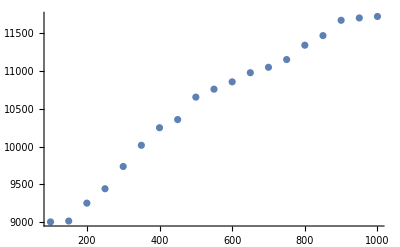

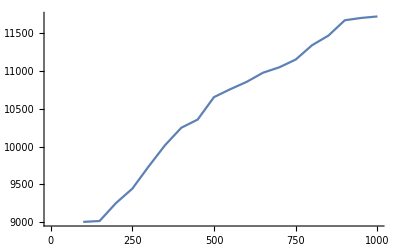

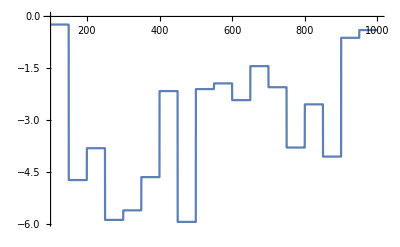

```mathematica
SetDirectory["/home/kempsilonnaught/Builds/CellSurfaceFE-master/CellSurfaceFE/MongeParameterization/FourthOrderSimpleTwoInclusion/gpls"];
ViewSurface[filename_] :=
Module[{stream,data,plot1,plot2},
stream = OpenRead[filename];
Skip[stream,Record,7];
data=ReadList[stream,{Number,Number,Number}];
Close[stream];
plot1=ListPlot3D[data,BoxRatios->Automatic];
plot2=ListPlot[Transpose[Drop[Transpose[data],-1]], PlotRange->{{ 0, 500}, {-500, 500}}];
{plot1,plot2}
]
files= FileNames[];
(*Print[files]*)

numbersInString[s_]:=ToExpression@StringCases[s,NumberString]
files = SortBy[files,numbersInString]
allPlots=Table[ViewSurface[file],{file,files}];
ListAnimate[allPlots]
SolveForce[filename_] :=
Module[{stream, data,force, forcefunction, forceplot, x},
stream = OpenRead[filename];
data = ReadList[stream,{Number,Number}];
Close[stream];
data
]
SetDirectory["/home/kempsilonnaught/Builds/CellSurfaceFE-master/CellSurfaceFE/MongeParameterization/FourthOrderSimpleTwoInclusion"]
Print[SolveForce["energysep.txt"]];
allData=SolveForce["energysep.txt"];
ListPlot[SolveForce["energysep.txt"], PlotRange->All]
ListPlot[allData,Joined->True]
force[x_]=-D[Interpolation[allData,InterpolationOrder->1][x],x];
Plot[force[x],{x,100, 1000}]
SetDirectory[StringJoin[NotebookDirectory[],"gpls/"]];
```

```mathematica
Norm[{1., -2.,2.1,2.11,2.111},2]
```

4.28